# Mathematica Cours 1

```mathematica
Quit[]
```

## Q 0

```mathematica
1+2
```

3

```mathematica
1+2;
```

## Q 1

```mathematica
Sum[1/(k*(k+1)),{k,1,n}]
```

1-1/(1+n)

```mathematica
Expand[(a+b)^(2)*(a-b)]
```

a^3+a^2 b-a b^2-b^3

```mathematica
Factor[a^3-b^3]
```

(a-b) (a^2+a b+b^2)

```mathematica
A:=1/(a-1)-1/(a+1)
```

```mathematica
Simplify[A]
```

2/(-1+a^2)

```mathematica
N[1/(Pi-1)-1/(Pi+1),1000]
```

0.2254891999190360053278255022785604372816947723837133639224013154436479227474162951958555435722099121374070206291366473940142855668306522248314581666819686888529220760487802018139376450602339972015395256093658922149120482771946062725076884567103737344071610548827914441106166387076741498085681784348157385633764054955366423128587079294841382305713172185584397264112058268077605754383259416409985393596097057855981749606690495877725794667409887892786806499816122348593594985876332876263885634641732922526936801847605647726829538390260178141108204853163000465137760421755380391397313229394007008487109470878234481860168243092446068773681586150268569693200198277107560709079737142328629580471284183298012279661348371035544887324432768185109392305002070351142496565009927484631353000764483931660307847845945559824154332697919691543227627320585009327792271041822945336040512115818192152952821318566061405481010999832670518030574029433960191102797377447369029481152552279449758175797827122461430772549407442

```mathematica
Expand[Sin[3*α]]
```

Sin[3 α]

## Q 2

```mathematica
f[x_]:=Exp[-1/x]/x
```

```mathematica
D[f[x],x]
```

ⅇ^(-1/x)/x^3-ⅇ^(-1/x)/x^2

```mathematica
Integrate[f[x],{x,1,2}]
```

ExpIntegralEi[-1]+Gamma[0,1/2]

```mathematica
Limit[f[x],x->+Infinity]
```

0

```mathematica
Limit[f[x],x->-Infinity]
```

0

```mathematica
Limit[f[x],x->0,Direction->-1]
```

0

```mathematica
Limit[f[x],x->0,Direction->1]
```

-∞

## Q 3

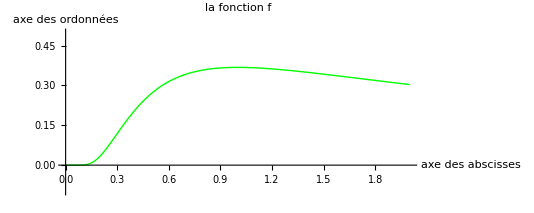

```mathematica
Plot[f[x],{x,0,2},
PlotRange->{-0.1,0.5},
PlotStyle->RGBColor[0,1,0],
Axes->True,
AxesLabel->{"axe des abscisses","axe des ordonnées"},
PlotLabel->"la fonction f",
AspectRatio->Automatic]
```